```mathematica
ClearAll["Global`*"];
(* Ciało o masie m=10 g wykonuje drgania harmoniczne o amplitudzie
A=10 cm i częstotliwości f. Sporządzić wykresy zależności od częstotliwości drgań maksymalnych wartości: siły zwracającej Fₓ,energii potencjalnej Eₚ, energii kinetycznej Eₖ. Sporządzić wykres zależności energii całkowitej drgań 
E_c=Eₚ+Eₖ od częstotliwości. Zakres częstotliwości przyjąć od 10 s⁻.b9 do 100 s⁻.b9. *)
```

```mathematica
x=A×Sin[ω×t+ϕ]
v=D[x, t]
a=D[v, t]
```

A Sin[ϕ+t ω]

A ω Cos[ϕ+t ω]

-A ω^2 Sin[ϕ+t ω]

```mathematica
r1=Solve[m×a==-k×x,k]
k=k/.r1[[1]]
```

{{k→m ω^2}}

m ω^2

```mathematica
Fxmax=m×a/.Sin[ϕ+ω×t]->1
Ekmax=(m×v^2)/2/.Cos[ϕ+ω×t]->1
Epmax=(k×x^2)/2/.Sin[ϕ+ω×t]->1
```

-A m ω^2

1/2 A^2 m ω^2

1/2 A^2 m ω^2

```mathematica
Ec=(m×v^2)/2+(k×x^2)/2//Simplify
```

1/2 A^2 m ω^2

```mathematica
m=10^-2;               (* kg *)
```

```mathematica
A=10^-1;                (* m *)
```

```mathematica
ω=2×π×f;
```

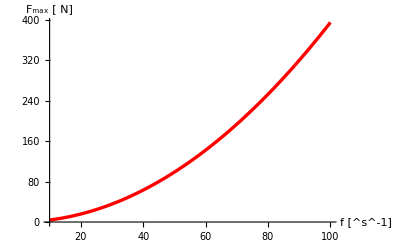

```mathematica
Plot[Abs[Fxmax],{f,10,100},
BaseStyle->{FontFamily->"Times",FontSlant->"Italic",FontSize->12},
 PlotStyle->{{RGBColor[1,0,0],Thickness[0.006]}},
AxesLabel->{"f  [^s^-1]","F_max [ N]"}]
```

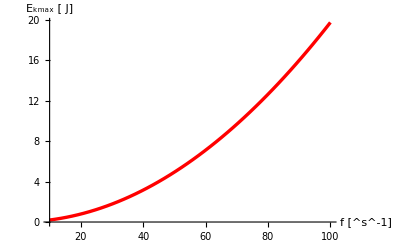

```mathematica
Plot[Ekmax,{f,10,100},
BaseStyle->{FontFamily->"Times",FontSlant->"Italic",FontSize->12},
 PlotStyle->{{RGBColor[1,0,0],Thickness[0.006]}},
AxesLabel->{"f  [^s^-1]","E_kmax [ J]"}]
```

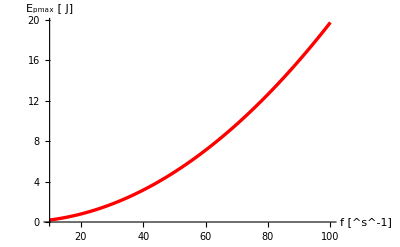

```mathematica
Plot[Epmax,{f,10,100},
BaseStyle->{FontFamily->"Times",FontSlant->"Italic",FontSize->12},
 PlotStyle->{{RGBColor[1,0,0],Thickness[0.006]}},
AxesLabel->{"f  [^s^-1]","E_pmax [ J]"}]
```

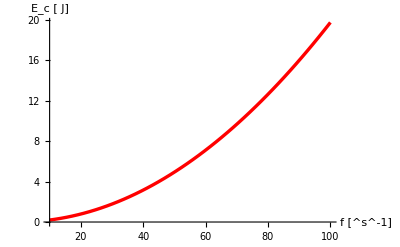

```mathematica
Plot[Ec,{f,10,100},
BaseStyle->{FontFamily->"Times",FontSlant->"Italic",FontSize->12},
 PlotStyle->{{RGBColor[1,0,0],Thickness[0.006]}},
AxesLabel->{"f  [^s^-1]","E_c [ J]"}]
```